```mathematica
delta=1;w=-1-delta;b=1;
points=ListPointPlot3D[{{b/(2*delta+3),b/(2*delta+3),b/(2*delta+3)},
{b/(delta+2),b/(delta+2),0},
{b/(delta+2),0,b/(delta+2)},
{0,b/(delta+2),b/(delta+2)},
{b,0,0},{0,b,0},{0,0,b}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{Style["\!\(\*SubscriptBox[\(x\),\(1\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(2\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(3\)]\)",FontSize->24]}]
```

-Graphics3D-

```mathematica
(*points=ListPointPlot3D[{{b,0,0},{b/(delta+2),b/(delta+2),0}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1}, PlotStyle->{Red,PointSize[0.02]}]*)
(*points=ListPointPlot3D[{{b/(2*delta+3),b/(2*delta+3),b/(2*delta+3)},{b/(delta+2),b/(delta+2),0}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1}, PlotStyle->{Red,PointSize[0.02]},AxesLabel->{Style["\!\(\*SubscriptBox[\(x\),\(1\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(2\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(3\)]\)",FontSize->24]}]*)
points=ListPointPlot3D[{{b,0,0},{b/(2*delta+3),b/(2*delta+3),b/(2*delta+3)}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1}, PlotStyle->{Red,PointSize[0.02]},AxesLabel->{Style["\!\(\*SubscriptBox[\(x\),\(1\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(2\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(3\)]\)",FontSize->24]}];
points=ListPointPlot3D[{{b/(delta+2),b/(delta+2),0},{b/(delta+2),0,b/(delta+2)}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1}, PlotStyle->{Red,PointSize[0.02]},AxesLabel->{Style["\!\(\*SubscriptBox[\(x\),\(1\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(2\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(3\)]\)",FontSize->24]}]
```

-Graphics3D-

```mathematica
pos[x_]:=If[x>0,x,0];
f1[x_,y_,z_,i_]=(-1)^i(-x+pos[w*y+w*z+b]);
f2[x_,y_,z_,i_]=(-1)^i(-y+pos[w*x+w*z+b]);
f3[x_,y_,z_,i_]=(-1)^i(-z+pos[w*x+w*y+b]);
f={f1,f2,f3};
```

```mathematica
eps=1/10;
allranges={{-eps,1+eps},{-eps,1+eps},{-eps,1+eps}};
ranges={{b/(delta+2)-eps,b/(delta+2)+eps},{b/(delta+2)-eps,b/(delta+2)+eps},{0-eps,0+eps}};
ranges={{b/(2*delta+3)-eps,b/(2*delta+3)+eps},{b/(2*delta+3)-eps,b/(2*delta+3)+eps},{b/(2*delta+3)-eps,b/(2*delta+3)+eps}}

ranges={{b/(2*delta+3)-eps,b/(delta+2)+eps},{b/(2*delta+3)-eps,b/(delta+2)+eps}, {0-eps,b/(2*delta+3)+eps}}(*F4&F7*)

ranges={{b/(delta+2)-eps,b/(delta+2)+eps},{0-eps/10,b/(delta+2)+eps},{0-1eps,b/(delta+2)+eps}}(*F4&F5*)

ranges={{b/(delta+2)-eps,b+eps},{0-eps,b/(delta+2)+eps},{0-eps,0+eps}}(*F1&F4*)
```

{{1/10,3/10},{1/10,3/10},{1/10,3/10}}

{{1/10,13/30},{1/10,13/30},{-1/10,3/10}}

{{7/30,13/30},{-1/100,13/30},{-1/10,13/30}}

{{7/30,11/10},{-1/10,13/30},{-1/10,1/10}}

```mathematica
As = Flatten[Table[Table[Reduce[Apply[f[[i]],Append[Table[If[k==i,ranges[[i]][[j]],x[k]],{k,3}],j+1]]<=0,Reals]&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]]),{j,2}],{i,3}]];
a=Table[RegionPlot3D[As[[i]],{x[1],ranges[[1]][[1]]-0.0001,ranges[[1]][[2]]+0.0001},{x[2],ranges[[2]][[1]]-0.0001,ranges[[2]][[2]]+0.0001}, {x[3],ranges[[3]][[1]]-0.0001,ranges[[3]][[2]]+0.0001},Mesh->None],{i,1}];
Bs1 = Flatten[Table[Table[Table[Reduce[Apply[f[[Mod[i+1,3]]],Append[Table[If[(k==i)||(k==Mod[i+1,3]),ranges[[k]][[If[k==i,j,n]]],x[k]],{k,3}],n+1]]<0,Reals]
&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]])
&&(If[Mod[n+1,2]==0,x[Mod[i+1,3]]<ranges[[Mod[i+1,3]]][[n]], x[Mod[i+1,3]]>ranges[[Mod[i+1,3]]][[n]]]),{j,2}],{i,3}],{n,2}]];
add=2;Bs2 = Flatten[Table[Table[Table[Reduce[Apply[f[[Mod[i+add,3]]],Append[Table[If[(k==i)||(k==Mod[i+add,3]),ranges[[k]][[If[k==i,j,n]]],x[k]],{k,3}],n+1]]<0,Reals]
&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]])
&&(If[Mod[n+1,2]==0,x[Mod[i+add,3]]<ranges[[Mod[i+add,3]]][[n]], x[Mod[i+add,3]]>ranges[[Mod[i+add,3]]][[n]]]),{j,2}],{i,3}],{n,2}]];kicsi=0.00000001;Bss=List[Bs1,Bs2];bbb=Table[Table[RegionPlot3D[Bss[[n]][[i]],{x[1],ranges[[1]][[1]]-kicsi,ranges[[1]][[2]]+kicsi},{x[2],ranges[[2]][[1]]-kicsi,ranges[[2]][[2]]+kicsi}, {x[3],ranges[[3]][[1]]-kicsi,ranges[[3]][[2]]+kicsi},AxesLabel->Automatic],{i,6}],{n,2}];
Cs= Flatten[Table[Table[Table[Table[If[Reduce[Apply[f[[n]],{ranges[[1]][[i]],ranges[[2]][[j]],ranges[[3]][[k]],If[n==1,i,If[n==2,j,k]]+1}]<0,Reals],{ranges[[1]][[i]],ranges[[2]][[j]],ranges[[3]][[k]]}],{i,2}],{j,2}],{k,2}],{n,3}],3];
c=ListPointPlot3D[Cs];
Show[a,bbb,c,points,AxesLabel->{Style["\!\(\*SubscriptBox[\(x\),\(1\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(2\)]\)",FontSize->24],Style["\!\(\*SubscriptBox[\(x\),\(3\)]\)",FontSize->24]}]
```

-Graphics3D-

```mathematica
ranges
```

{{103/300,101/100},{1/2,101/100},{1/2,101/100}}

```mathematica
f1
```

```mathematica
f1[11/10,-1/10,-1/10,0]
```

3/10

```mathematica
3/10 goes outside
```

```mathematica
f2[11/10,-1/10,-1/10,0]
```

1/10

```mathematica
f3[11/10,-1/10,-1/10,0]
```

1/10

```mathematica
f1[7/30,13/30,-1/10,0]
```

1/10

```mathematica
f2[7/30,13/30,-1/10,0]
```

```mathematica
3/10 goes outside
```

```mathematica
f3[7/30,13/30,-1/10,0]
```

1/10

```mathematica
As
```

{x[2]≥1/300 (103-300 x[3]),x[2]≤1/300 (97-300 x[3]),False,x[1]≤1/300 (97-300 x[3]),False,x[1]≤1/300 (97-300 x[2])}

```mathematica
As = Flatten[Table[Table[Reduce[Apply[f[[i]],Append[Table[If[k==i,ranges[[i]][[j]],x[k]],{k,3}],j+1]]<=0,Reals],{j,2}],{i,3}]];
```

```mathematica
Reduce[As[[1]]&&(ranges[[2]][[1]]<x[2]<ranges[[2]][[2]])&&
(ranges[[3]][[1]]<x[3]<ranges[[3]][[2]]),Reals]
```

-1/20<x[3]<13/30&&1/60 (23-60 x[3])≤x[2]<13/30

```mathematica
As
```

{x[2]≥1/60 (23-60 x[3]),x[2]≤1/60 (17-60 x[3]),False,x[1]≤1/60 (17-60 x[3]),False,x[1]≤1/60 (17-60 x[2])}

```mathematica
Mod[3+1,3]+1
```

2

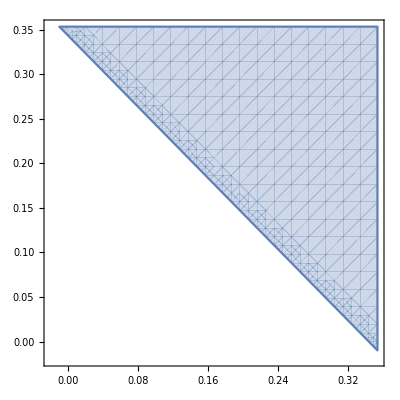

```mathematica
RegionPlot[Reduce[As[[1]]&&(ranges[[2]][[1]]<x[2]<ranges[[2]][[2]])&&
(ranges[[3]][[1]]<x[3]<ranges[[3]][[2]]),Reals],{x[2],ranges[[2]][[1]],ranges[[2]][[2]]},{x[3],ranges[[3]][[1]],ranges[[3]][[2]]}]
```

```mathematica
As = Flatten[Table[Table[Reduce[Apply[f[[i]],Append[Table[If[k==i,ranges[[i]][[j]],x[k]],{k,3}],j+1]]==0,Reals]&&(If[Mod[j+1,2]==0,x[i]==ranges[[i]][[j]], x[i]==ranges[[i]][[j]]]),{j,2}],{i,3}]];
```

```mathematica
As[[1]]
```

x[2]==1/60 (23-60 x[3])&&x[1]==7/30

```mathematica
Plot[{f2[7/30,1/60 (23-60 x[3]),x[3],0],f3[7/30,1/60 (23-60 x[3]),x[3],0]},{x[3],ranges[[3]][[1]],ranges[[3]][[2]]},PlotLabels->{"f2","f3"}]
```